Зад. 1 Функцията на Рунге f(x) = 1/(1+25 x^2) е апроксимирана с полиномите:
p_4(x) = 1 - 4.22719 x^2+3.31565 x^4 
и
p_10(x)=1 - 16.8552 x^2+123.36 x^4-381.434 x^6+494.91 x^8-220.942 x^10.

Да се намерят и сравянт рваномерните и средноквадратичните разстояния при тегло μ(x) = 1 в интервала [-1,1] между f и двата полнома.

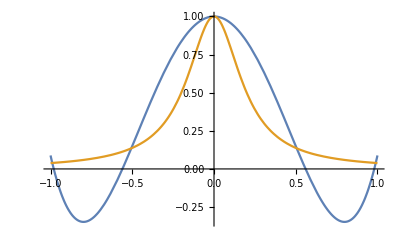

```mathematica
Plot[{1-4.22719 x^2+3.31565 x^4,1/(1+25 x^2)},{x,-1,1}]
```

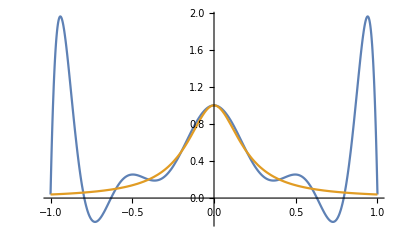

```mathematica
Plot[{1-16.8552 x^2+123.36 x^4-381.434 x^6+494.91 x^8-220.942 x^10,1/(1+25 x^2)},{x,-1,1}]
```

Зад. 2 Да се намери полиномът на най-добро средноквадратично приближение от втора степен в интервала [0, 1.5] за функцията f(x) = e^x при тегло μ(x) = 1.

Зад. 3 Като се използва факта, че най-доброто решение x на преопределената система А x = b,
удовлетворява матричното уравнение 

A^Т A x = А^Тb,

да се реши системата
x - y = 1
x + y = 1
x + y = -1
x - y = -1.

```mathematica
(*Exercise 1*)
```

```mathematica
f[x_] = 1/(1+25 x^2);
p[x_] = 1 - 4.22719 x^2+3.31565 x^4;
ro[x_] = Abs[f[x]-p[x]] ;
result = Maximize[ro[x],0≤ x≤1,x]
{0.40697315836367476,{x->0.7897907842410147}}
```

```mathematica
pT[x]=1 - 16.8552 x^2+123.36 x^4-381.434 x^6+494.91 x^8-220.942 x^10;
roT[x_] =  Abs[f[x]-pT[x]] ;
resultT = Maximize[roT[x],0≤ x≤1,x]
{1.9159171011388616,{x->0.9402204905690202}} (*Shows us the max error in the given interval*)
maxDiffWithOtherFormula = (Integrate[(f[x]-p[x])^2,{x,-1,1}])^(1/2);
maxDiffWithOtherFormulaT= (Integrate[(f[x]-pT[x])^2,{x,-1,1}])^(1/2); (*Shows us average error in the interval*)
maxDiffWithOtherFormula
maxDiffWithOtherFormulaT
0.26589565731254844
0.8209050258906632
```

```mathematica
(*Exercise 2*)
```

```mathematica
p[x_]= a*x^2+b*x+c;
maxDiffWithOtherFormulaT[a_,b_,c_]:= (Integrate[(E^x-p[x])^2,{x,0,1.5}])^(1/2);
```

```mathematica
derivA[a_,b_,c_] = D[maxDiffWithOtherFormulaT[a,b,c], a];
derivB[a_,b_,c_] = D[maxDiffWithOtherFormulaT[a,b,c], b];
derivC[a_,b_,c_] = D[maxDiffWithOtherFormulaT[a,b,c], c];
```

```mathematica
derA[a,b,c]
(-7.204222675845161+3.0375 a+2.53125 b+2.25 c)/(2 √(9.542768461593834+1.51875 a^2+1.125 b^2-6.963378140676129 c+1.5 c^2+b (-6.4816890703380645+2.25 c)+a (-7.204222675845161+2.53125 b+2.25 c)))
```

```mathematica
ABC = Solve[{derA[a,b,c] == 0, derB[a,b,c]==0,derC[a,b,c]==0},{a,b,c}];
```

```mathematica
ABC
{{a->1.101699236641322,b->0.5859497491819602,c->1.055389307524581}}
```

```mathematica
result[x_]= p[x]/.ABC[[1]]
1.055389307524581+0.5859497491819602 x+1.101699236641322 x^2
```